```mathematica
SetOptions[MatrixPlot,PlotRange->{0,1},ColorFunction->GrayLevel,FrameTicks->False];
SetOptions[ListContourPlot,{PlotRange->All,ColorFunction->(ColorData["GrayTones",(1-#)]&)},FrameTicks->False];
(* x -> a number represented as a string of n digits *)
df[n_,x_]:=StringJoin[ToString/@Join[ConstantArray[0,n-Floor@Log[10,x]-1],IntegerDigits[x]]]
```

## Double Vortex Background

```mathematica
len=50;
dx=1.;
σ=len/6;
steps=12000;
dt=dx^2/10;
T=dt * steps;
outfigs=200;
outstep=steps/outfigs;
kappa=.05;
```

```mathematica
map2[f_,data_]:=Map[f,data,{2}]
```

```mathematica
exp1=map2[.5 Exp[-((#[[1]]-len/4)^2+(#[[2]]-len/4)^2)/(2 σ^2)]&,Partition[Tuples[Range[len],2],len]];
vortx1=map2[{-(#[[2]]-len/4)/(√((#[[1]]-len/4)^2+(#[[2]]-len/4)^2+.01)),(#[[1]]-len/4)/(√((#[[1]]-len/4)^2+(#[[2]]-len/4)^2+.01))}&,Partition[Tuples[Range[len],2],len]];
exp2=map2[.5 Exp[-((#[[1]]-3len/4)^2+(#[[2]]-3len/4)^2)/(2 σ^2)]&,Partition[Tuples[Range[len],2],len]];
vortx2=map2[{(#[[2]]-3len/4)/(√((#[[1]]-3len/4)^2+(#[[2]]-3len/4)^2+.01)),-(#[[1]]-3len/4)/(√((#[[1]]-3len/4)^2+(#[[2]]-3len/4)^2+.01))}&,Partition[Tuples[Range[len],2],len]];
```

```mathematica
vel=exp1 vortx1+exp2 vortx2;
```

```mathematica
temp=map2[Exp[-((#[[1]]-3len/8)^2+(#[[2]]-3len/8)^2)/(2 1.4)]&,Partition[Tuples[Range[len],2],len]];
```

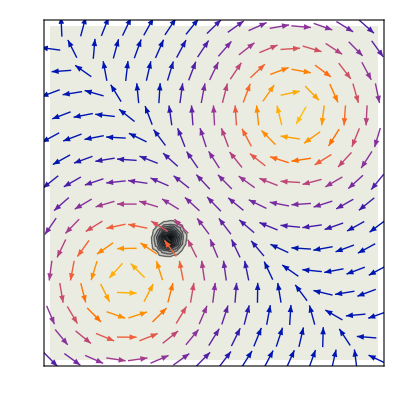

```mathematica
Show[ListContourPlot[temp],ListVectorPlot[vel]]
```

```mathematica
Clear[exp1,exp2,vortx1,vortx2];
```

```mathematica
TransportEvol[temp_,vel_]:=kappa/dx^2(RotateLeft[temp,{0,1}]+RotateLeft[temp,{0,-1}]+RotateLeft[temp,{1,0}]+RotateLeft[temp,{-1,0}]-4 temp)-1/(2 dx)vel[[All,All,1]](RotateLeft[temp,{1,0}]-RotateLeft[temp,{-1,0}])-1/(2 dx)vel[[All,All,2]](RotateLeft[temp,{0,1}]-RotateLeft[temp,{0,-1}])
```

```mathematica
(* Euler step *)
data=Join[{temp,temp+dt TransportEvol[temp,vel]}];
data//Dimensions
```

{2,50,50}

```mathematica
Euler[temp_]:=temp+dt TransportEvol[temp,vel];
AB2[data_]:=With[{s=data[[2]]+1.5 dt TransportEvol[data[[2]],vel]-.5 dt TransportEvol[data[[1]],vel]},Join[{data[[2]],If[Max[s]>1,s/Max[s],s] }]];
```

```mathematica
(* Euler evolution *)
(plots=Reap[Do[Sow[temp=Euler[temp],Mod[i,outstep]],{i,1,steps}],1][[2,1]])//Timing//First
```

$Aborted

```mathematica
(plots=Reap[Do[Sow[data=AB2[data],Mod[i,outstep]],{i,1,steps}],1][[2,1]])//Timing//First
```

344.731

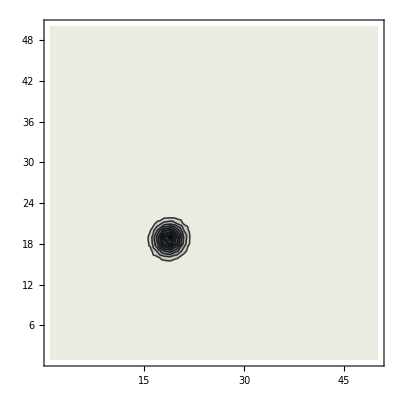
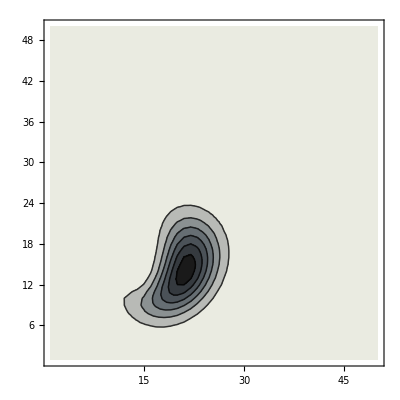
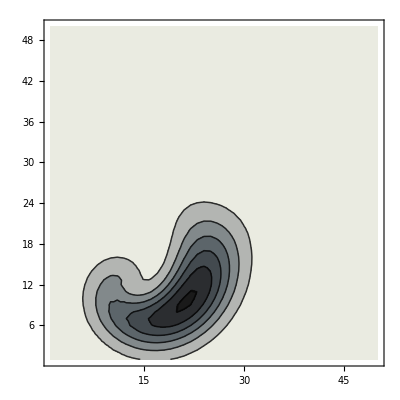
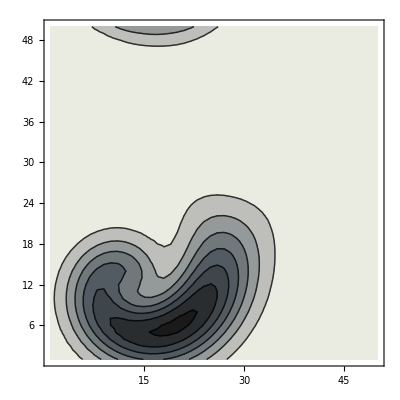
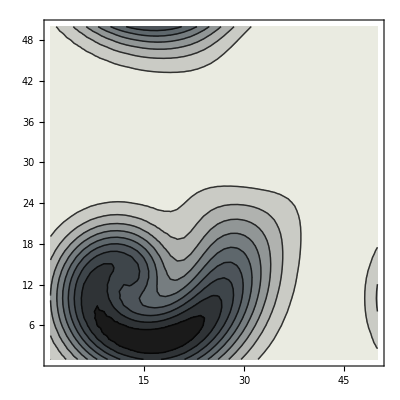
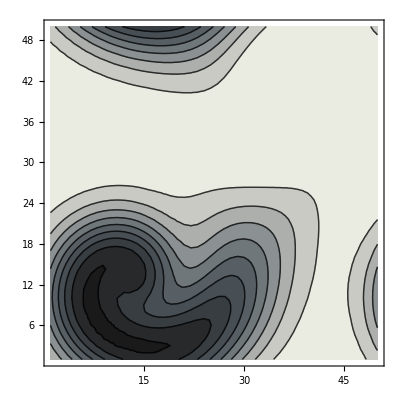
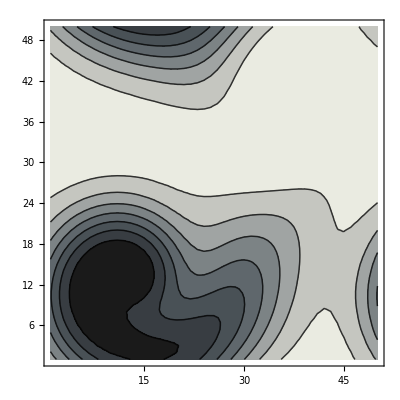
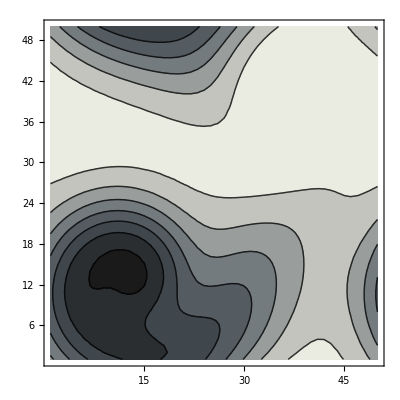

```mathematica
(* use only for testing, with a small number of plots *)
ListContourPlot/@plots
```

```mathematica
Export["/home/gabriel/Documents/HeatAnimation/transport/gauss_smallkappa_"<>df[Floor@Log[10,steps]+1,#]<>".png",ListContourPlot@plots[[#]]]&/@Range[Length@plots];
```

```mathematica
Export["/home/gabriel/Documents/HeatAnimation/transport_vfield/gauss_dblvrtx_velf_"<>df[Floor@Log[10,steps]+1,#]<>".png",Show[ListContourPlot@plots[[#]],ListVectorPlot[vel]]]&/@Range[Length@plots];
```

## Double Vortex Background + Painting

```mathematica
(*img=ImageData[Import["/home/gabriel/Documents/HeatAnimation/scream.jpeg"]];*)
img=ImageData[Import["/home/gabriel/Documents/HeatAnimation/pineaplebud.jpg"]];
```

```mathematica
len=50;
dx=1.;
σ=len/6;
steps=40000;
dt=dx^2/100;
T=dt * steps;
outfigs=200;
outstep=steps/outfigs;
kappa=.01;
```

```mathematica
map2[f_,data_]:=Map[f,data,{2}]
```

```mathematica
temp=img[[1;;;;10,1;;;;10,1]];
With[{s=temp//Dimensions},lenx=s[[1]];leny=s[[2]];Print[s]]
```

{180,155}

```mathematica
exp1=map2[.5 Exp[-((#[[1]]-lenx/4)^2+(#[[2]]-leny/4)^2)/(2 σ^2)]&,Partition[Tuples[{Range[lenx],Range[leny]}],leny]];
vortx1=map2[{-(#[[2]]-lenx/4)/(√((#[[1]]-lenx/4)^2+(#[[2]]-leny/4)^2+.01)),(#[[1]]-leny/4)/(√((#[[1]]-lenx/4)^2+(#[[2]]-leny/4)^2+.01))}&,Partition[Tuples[{Range[lenx],Range[leny]}],leny]];
exp2=map2[.5 Exp[-((#[[1]]-3lenx/4)^2+(#[[2]]-3leny/4)^2)/(2 σ^2)]&,Partition[Tuples[{Range[lenx],Range[leny]}],leny]];
vortx2=map2[{(#[[2]]-3lenx/4)/(√((#[[1]]-3lenx/4)^2+(#[[2]]-3leny/4)^2+.01)),-(#[[1]]-3leny/4)/(√((#[[1]]-3lenx/4)^2+(#[[2]]-3leny/4)^2+.01))}&,Partition[Tuples[{Range[lenx],Range[leny]}],leny]];
```

```mathematica
vel=exp1 vortx1+exp2 vortx2;
```

```mathematica
Clear[exp1,exp2,vortx1,vortx2];
```

```mathematica
TransportEvol[temp_,vel_]:=kappa/dx^2(RotateLeft[temp,{0,1}]+RotateLeft[temp,{0,-1}]+RotateLeft[temp,{1,0}]+RotateLeft[temp,{-1,0}]-4 temp)-1/(2 dx)vel[[All,All,1]](RotateLeft[temp,{1,0}]-RotateLeft[temp,{-1,0}])-1/(2 dx)vel[[All,All,2]](RotateLeft[temp,{0,1}]-RotateLeft[temp,{0,-1}])
```

```mathematica
(* Euler step *)
data=Join[{temp,temp+dt TransportEvol[temp,vel]}];
data//Dimensions
```

{2,180,155}

```mathematica
Euler[temp_]:=temp+dt TransportEvol[temp,vel];
AB2[data_]:=With[{s=data[[2]]+1.5 dt TransportEvol[data[[2]],vel]-.5 dt TransportEvol[data[[1]],vel]},Join[{data[[2]],If[Max[s]>1,s/Max[s],s] }]];
```

```mathematica
(plots=Reap[Do[Sow[Last[data=AB2[data]],Mod[i,outstep]],{i,1,steps}],1][[2,1]])//Timing//First
```

1517.92

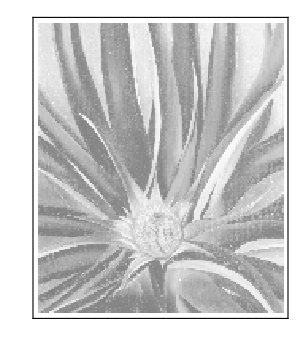
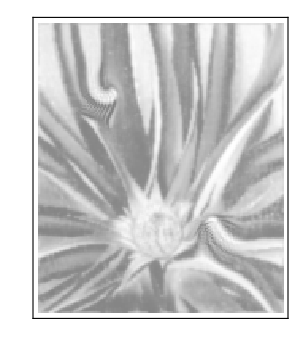
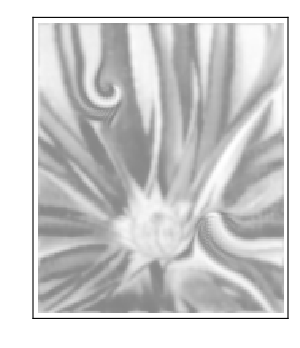
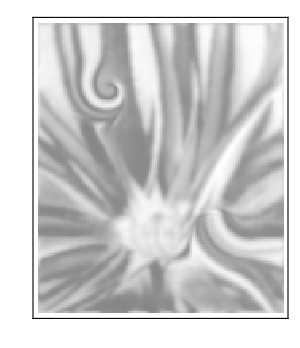
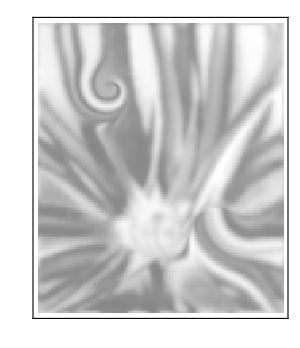
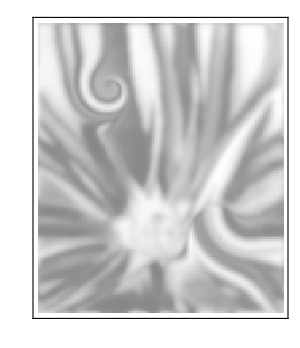
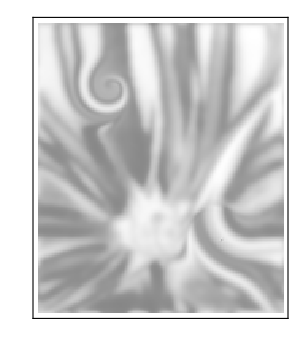
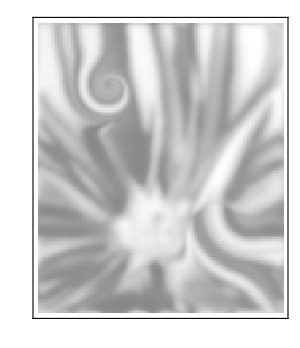

```mathematica
(* use only for testing, with a small number of plots *)
MatrixPlot/@plots[[1;;;;20]]
```

```mathematica
Export["/home/gabriel/Documents/HeatAnimation/transport/pineapplebud_"<>df[Floor@Log[10,steps]+1,#]<>".png",MatrixPlot@plots[[#]]]&/@Range[Length@plots];
```

## Hybrid Explicit-Implicit Transport

Convection-diffusion equation. Diffusion term is evolved with an Alternating Direction Implicit Method. Convection term is evolved with explicit 2nd order upwind algorithm.

```mathematica
(*img=ImageData[Import["/home/gabriel/Documents/HeatAnimation/scream.jpeg"]];*)
img=ImageData[Import["/home/gabriel/Documents/HeatAnimation/pineaplebud.jpg"]];
```

```mathematica
dx=1;
steps=4000;
dt=dx^2/40;
T=dt * steps;
outfigs=200; (* must be smaller than steps *)
outstep=steps/outfigs;
κ=.01;
```

```mathematica
map2[f_,data_]:=Map[f,data,{2}]
```

```mathematica
temp=img[[1;;;;10,1;;;;10,1]];
With[{s=temp//Dimensions},lenx=s[[1]];leny=s[[2]];σ=lenx/6;Print[s]]
```

{180,155}

```mathematica
exp1=map2[.5 Exp[-((#[[1]]-lenx/4)^2+(#[[2]]-leny/4)^2)/(2 σ^2)]&,Partition[Tuples[{Range[lenx],Range[leny]}],leny]];
vortx1=map2[{-(#[[2]]-lenx/4)/(√((#[[1]]-lenx/4)^2+(#[[2]]-leny/4)^2+.01)),(#[[1]]-leny/4)/(√((#[[1]]-lenx/4)^2+(#[[2]]-leny/4)^2+.01))}&,Partition[Tuples[{Range[lenx],Range[leny]}],leny]];
exp2=map2[.5 Exp[-((#[[1]]-3lenx/4)^2+(#[[2]]-3leny/4)^2)/(2 σ^2)]&,Partition[Tuples[{Range[lenx],Range[leny]}],leny]];
vortx2=map2[{(#[[2]]-3lenx/4)/(√((#[[1]]-3lenx/4)^2+(#[[2]]-3leny/4)^2+.01)),-(#[[1]]-3leny/4)/(√((#[[1]]-3lenx/4)^2+(#[[2]]-3leny/4)^2+.01))}&,Partition[Tuples[{Range[lenx],Range[leny]}],leny]];
```

```mathematica
vel=exp1 vortx1+exp2 vortx2;
```

```mathematica
Clear[exp1,exp2,vortx1,vortx2];
```

```mathematica
TransportEvol[temp_,vel_]:=kappa/dx^2(RotateLeft[temp,{0,1}]+RotateLeft[temp,{0,-1}]+RotateLeft[temp,{1,0}]+RotateLeft[temp,{-1,0}]-4 temp)-1/(2 dx)vel[[All,All,1]](RotateLeft[temp,{1,0}]-RotateLeft[temp,{-1,0}])-1/(2 dx)vel[[All,All,2]](RotateLeft[temp,{0,1}]-RotateLeft[temp,{0,-1}])
```

```mathematica
ADI[data_]:=Block[{phi},
phi=(2/dt-κ/dx^2)data+κ/(2 dx^2)RotateLeft[data,{0,1}]+κ/(2 dx^2)RotateLeft[data,{0,-1}]-1/(2 dx) map2[Max[#[[1]],0]&,vel](3data-4RotateLeft[data,{1,0}]+RotateLeft[data,{2,0}])-1/(2dx)map2[Min[#[[1]],0]&,vel](-3data+4RotateLeft[data,{-1,0}]-RotateLeft[data,{-2,0}])-1/(2dx)map2[Max[#[[2]],0]&,vel](3data-4RotateLeft[data,{0,1}]+RotateLeft[data,{0,2}])-1/(2dx)map2[Min[#[[2]],0]&,vel](-3data+4RotateLeft[data,{0,-1}]-RotateLeft[data,{0,-2}]);
phi=Transpose[LinearSolve[By,#]&/@Transpose[phi]];
phi=(2/dt-2/dx^2)phi+κ/(2 dx^2)RotateLeft[phi,{1,0}]+κ/(2 dx^2)RotateLeft[phi,{-1,0}]-1/(2 dx) map2[Max[#[[1]],0]&,vel](3phi-4RotateLeft[phi,{1,0}]+RotateLeft[phi,{2,0}])-1/(2dx)map2[Min[#[[1]],0]&,vel](-3phi+4RotateLeft[phi,{-1,0}]-RotateLeft[phi,{-2,0}])-1/(2dx)map2[Max[#[[2]],0]&,vel](3phi-4RotateLeft[phi,{0,1}]+RotateLeft[phi,{0,2}])-1/(2dx)map2[Min[#[[2]],0]&,vel](-3phi+4RotateLeft[phi,{0,-1}]-RotateLeft[phi,{0,-2}]);
LinearSolve[Bx,#]&/@phi];
```

```mathematica
(* matrices for the implicit method, one corresponds to the y half-step, another to the x half-step *)
By=SparseArray[{{i_,i_}->2/dt+κ/dx^2,{i_,j_}/;Abs[i-j]==1->-κ/(2 dx^2)},{lenx,lenx}];
Bx=SparseArray[{{i_,i_}->2/dt+κ/dx^2,{i_,j_}/;Abs[i-j]==1->-κ/(2 dx^2)},{leny,leny}];
```

```mathematica
Euler[temp_]:=temp+dt ADI[temp];
```

```mathematica
(plots=Reap[Do[Sow[temp=ADI[temp],Mod[i,outstep]],{i,1,steps}],1][[2,1]])//Timing//First
```

970.066

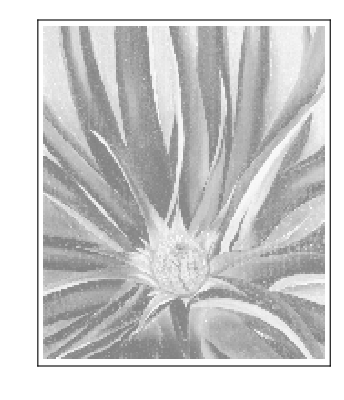
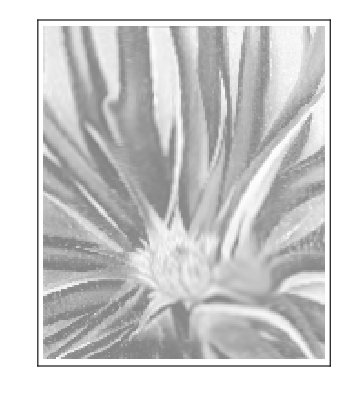
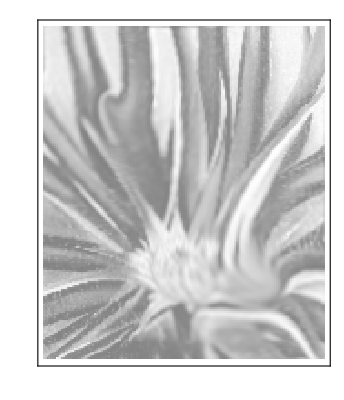
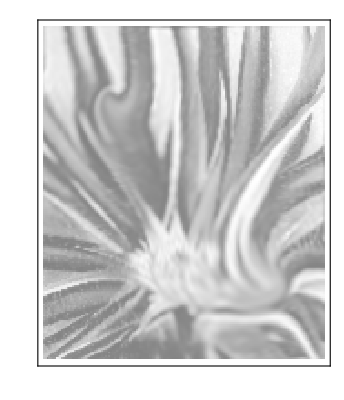
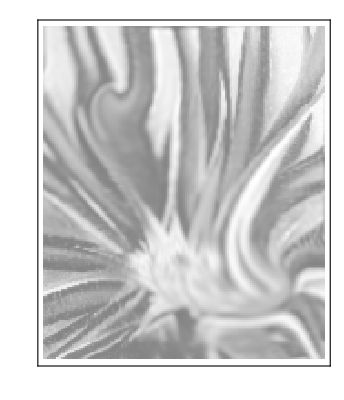
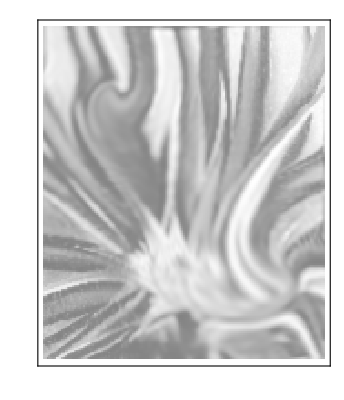
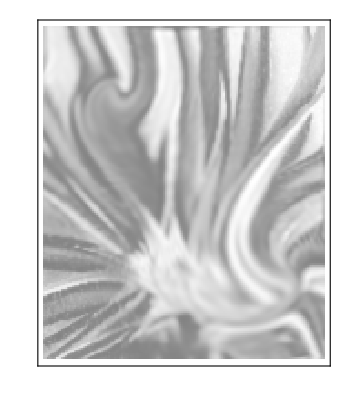
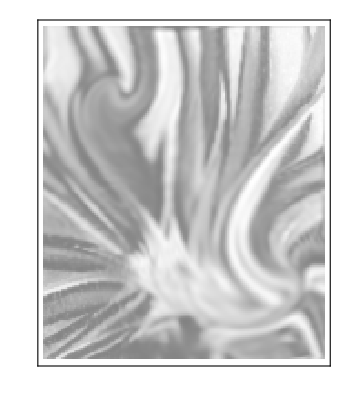

```mathematica
MatrixPlot/@plots
```

```mathematica
Export["/home/gabriel/Documents/HeatAnimation/transport/pineapplebud_expimp_"<>df[Floor@Log[10,steps]+1,#]<>".png",MatrixPlot@plots[[#]]]&/@Range[Length@plots];
```

## Hybrid Explicit-Implicit Transport, Colors

Convection-diffusion equation. Diffusion term is evolved with an Alternating Direction Implicit Method. Convection term is evolved with explicit 2nd order upwind algorithm.

```mathematica
(*img=ImageData[Import["/home/gabriel/Documents/HeatAnimation/scream.jpeg"]];*)
img=ImageData[Import["/home/gabriel/Documents/HeatAnimation/pineaplebud.jpg"]];
```

```mathematica
dx=1;
steps=4000;
dt=dx^2/40;
T=dt * steps;
outfigs=200; (* must be smaller than steps *)
outstep=steps/outfigs;
κ=.01;
```

```mathematica
map2[f_,data_]:=Map[f,data,{2}]
```

```mathematica
temp=img[[1;;;;8,1;;;;8,1]];
With[{s=temp//Dimensions},lenx=s[[1]];leny=s[[2]];σ=lenx/6;Print[s]]
```

{225,193}

```mathematica
exp1=map2[.5 Exp[-((#[[1]]-lenx/4)^2+(#[[2]]-leny/4)^2)/(2 σ^2)]&,Partition[Tuples[{Range[lenx],Range[leny]}],leny]];
vortx1=map2[{-(#[[2]]-lenx/4)/(√((#[[1]]-lenx/4)^2+(#[[2]]-leny/4)^2+.01)),(#[[1]]-leny/4)/(√((#[[1]]-lenx/4)^2+(#[[2]]-leny/4)^2+.01))}&,Partition[Tuples[{Range[lenx],Range[leny]}],leny]];
exp2=map2[.5 Exp[-((#[[1]]-3lenx/4)^2+(#[[2]]-3leny/4)^2)/(2 σ^2)]&,Partition[Tuples[{Range[lenx],Range[leny]}],leny]];
vortx2=map2[{(#[[2]]-3lenx/4)/(√((#[[1]]-3lenx/4)^2+(#[[2]]-3leny/4)^2+.01)),-(#[[1]]-3leny/4)/(√((#[[1]]-3lenx/4)^2+(#[[2]]-3leny/4)^2+.01))}&,Partition[Tuples[{Range[lenx],Range[leny]}],leny]];
```

```mathematica
vel=exp1 vortx1+exp2 vortx2;
```

```mathematica
Clear[exp1,exp2,vortx1,vortx2];
```

```mathematica
TransportEvol[temp_,vel_]:=kappa/dx^2(RotateLeft[temp,{0,1}]+RotateLeft[temp,{0,-1}]+RotateLeft[temp,{1,0}]+RotateLeft[temp,{-1,0}]-4 temp)-1/(2 dx)vel[[All,All,1]](RotateLeft[temp,{1,0}]-RotateLeft[temp,{-1,0}])-1/(2 dx)vel[[All,All,2]](RotateLeft[temp,{0,1}]-RotateLeft[temp,{0,-1}])
```

```mathematica
(* matrices for the implicit method, one corresponds to the y half-step, another to the x half-step *)
By=SparseArray[{{i_,i_}->2/dt+κ/dx^2,{i_,j_}/;Abs[i-j]==1->-κ/(2 dx^2)},{lenx,lenx}];
Bx=SparseArray[{{i_,i_}->2/dt+κ/dx^2,{i_,j_}/;Abs[i-j]==1->-κ/(2 dx^2)},{leny,leny}];
```

```mathematica
ADI[data_]:=Block[{phi},
phi=(2/dt-κ/dx^2)data+κ/(2 dx^2)RotateLeft[data,{0,1}]+κ/(2 dx^2)RotateLeft[data,{0,-1}]-1/(2 dx) map2[Max[#[[1]],0]&,vel](3data-4RotateLeft[data,{1,0}]+RotateLeft[data,{2,0}])-1/(2dx)map2[Min[#[[1]],0]&,vel](-3data+4RotateLeft[data,{-1,0}]-RotateLeft[data,{-2,0}])-1/(2dx)map2[Max[#[[2]],0]&,vel](3data-4RotateLeft[data,{0,1}]+RotateLeft[data,{0,2}])-1/(2dx)map2[Min[#[[2]],0]&,vel](-3data+4RotateLeft[data,{0,-1}]-RotateLeft[data,{0,-2}]);
phi=Transpose[LinearSolve[By,#]&/@Transpose[phi]];
phi=(2/dt-2/dx^2)phi+κ/(2 dx^2)RotateLeft[phi,{1,0}]+κ/(2 dx^2)RotateLeft[phi,{-1,0}]-1/(2 dx) map2[Max[#[[1]],0]&,vel](3phi-4RotateLeft[phi,{1,0}]+RotateLeft[phi,{2,0}])-1/(2dx)map2[Min[#[[1]],0]&,vel](-3phi+4RotateLeft[phi,{-1,0}]-RotateLeft[phi,{-2,0}])-1/(2dx)map2[Max[#[[2]],0]&,vel](3phi-4RotateLeft[phi,{0,1}]+RotateLeft[phi,{0,2}])-1/(2dx)map2[Min[#[[2]],0]&,vel](-3phi+4RotateLeft[phi,{0,-1}]-RotateLeft[phi,{0,-2}]);
LinearSolve[Bx,#]&/@phi];
```

```mathematica
Euler[temp_]:=temp+dt ADI[temp];
```

```mathematica
(plots1=Reap[Do[Sow[temp=ADI[temp],Mod[i,outstep]],{i,1,steps}],1][[2,1]])//Timing//First
```

1483.16

```mathematica
temp=img[[1;;;;8,1;;;;8,2]];
(plots2=Reap[Do[Sow[temp=ADI[temp],Mod[i,outstep]],{i,1,steps}],1][[2,1]])//Timing//First
```

1502.24

```mathematica
temp=img[[1;;;;8,1;;;;8,3]];
(plots3=Reap[Do[Sow[temp=ADI[temp],Mod[i,outstep]],{i,1,steps}],1][[2,1]])//Timing//First
```

1417.03

```mathematica
plots1=plots1/(Max/@plots1);
plots2=plots2/(Max/@plots2);
plots3=plots3/(Max/@plots3);
```

```mathematica
Export["/home/gabriel/Documents/HeatAnimation/pineapplebud/expimp_"<>df[Floor@Log[10,steps]+1,#]<>".png",Image[Transpose[{plots1[[#]],plots2[[#]],plots3[[#]]},{3,1,2}]]]&/@Range[Length@plots1];
```